```mathematica
(*4.15*)
```

```mathematica
s=1;
xNodes=Table[(i-1)/s,{i,1,s+1}];
LagrangeBasis[i_,x_, nodes_]:=Product[(x-nodes[[j]])/(nodes[[i]]-nodes[[j]]),{j,DeleteCases[Range[1,s+1],i]}];
Ke[nodes_]:=Table[Integrate[D[LagrangeBasis[i,x,nodes],x]* D[LagrangeBasis[j,x,nodes],x],{x,nodes[[1]],nodes[[s+1]]}],{i,1,s+1},{j,1,s+1}];
fe[nodes_]:=Table[Integrate[LagrangeBasis[i,x,nodes],{x,nodes[[1]],nodes[[s+1]]}],{i,1,s+1}];
Ke[xNodes] // MatrixForm
fe [xNodes] // MatrixForm
```

(1 | -1
-1 | 1)

(1/2
1/2)

{-2 (-1/2+x),-2 (-1+x)}

{1,-53/40,-313/140}

53/20 (-1+x)-2 (-1/2+x)

313/70 (-1+x)+53/20 (-1/2+x)

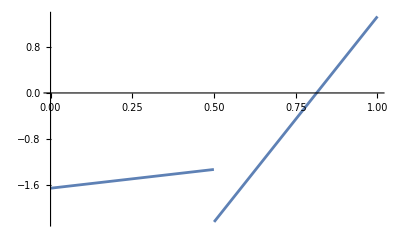

(5/2 | -5/2
-5/2 | 5/2)

(7/2 | -7/2
-7/2 | 7/2)

(1 | 0 | 0
-5/2 | 6 | -7/2
0 | -7/2 | 7/2)

(1
-21/8
-51/16)

{1.,-1.325,-2.23571}

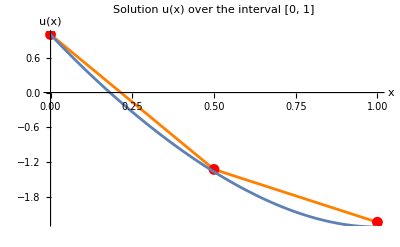

(7/2 | -7/2
-7/2 | 7/2)

(1 | 0 | 0
-5/2 | 6 | -7/2
0 | -7/2 | 7/2)

(1
-21/8
-51/16)

{1.,-1.325,-2.23571}

-Graphics-

```mathematica
(*4.16*)
n=2; 
s =1;
nodes=Table[i/n,{i,0,n}]; 
a[x_]:=1+x;
f[x_]:=-18 x^2; 
LagrangeBasis[i_,x_, nodes_]:=Product[(x-nodes[[j]])/(nodes[[i]]-nodes[[j]]),{j,DeleteCases[Range[1,s+1],i]}];
Ke[nodes_]:=Table[Integrate[a[x]*D[LagrangeBasis[i,x,nodes],x]* D[LagrangeBasis[j,x,nodes],x],{x,nodes[[1]],nodes[[s+1]]}],{i,1,s+1},{j,1,s+1}];
fe[nodes_]:=Table[Integrate[f[x]*LagrangeBasis[i,x,nodes],{x,nodes[[1]],nodes[[s+1]]}],{i,1,s+1}];
globalKe=ConstantArray[0,{(n*s)+1,(n*s)+1}];
globalFe=ConstantArray[0,(n*s)+1];
fis = {};
matrixes = {};
For[e=1, e<=n, e++,
mainNodes={nodes[[e]],nodes[[e+1]]};
elementNodes=Table[mainNodes[[1]]+(mainNodes[[2]]-mainNodes[[1]])*(i/s),{i,0,s}];
AppendTo[fis, LagrangeBasis[s,x,elementNodes]];
AppendTo[matrixes, Ke[elementNodes]];
globalIndices=Range[(e-1)*s+1,e*s+1];
globalKe[[globalIndices,globalIndices]]+=Ke[elementNodes];
globalFe[[globalIndices]]+=fe[elementNodes];]
globalKe[[1,1]]=1;
globalKe[[1,2;;]]=0;
globalFe[[1]]=1;
globalKe[[-1, -1]] +=0;
globalFe[[-1]] += 0;

u=LinearSolve[globalKe,globalFe];
fis
u
Ue[1]= u[[1]]*fis[[1]] + u[[2]]*fis[[2]]
Ue[2] = u[[2]]*fis[[1]] + u[[3]]*fis[[2]]
p1 = Plot[Ue[1], {x, 0, 0.5}];
p2 = Plot[Ue[2], {x, 0.5, 1}];
UePiecewise=Piecewise[{{Ue[1],0<=x<=0.5},{Ue[2],0.5<=x<=1}}];

(*Plot the piecewise solution*)
Plot[UePiecewise,{x,0,1}]

Table[i/(n*s),{i, 0,n*s}];
plotu =ListLinePlot[Transpose[{Table[i/(n*s),{i, 0,n*s}],u}],PlotRange->All,PlotLabel->"Solution u(x) over the interval [0, 1]",AxesLabel->{"x","u(x)"},PlotStyle->Orange,PlotStyle->Thick,Mesh->All,MeshStyle->Red];

deqn=-D[(1+x) D[c[x],x],x]==-18 x^2;
bc={c[0]==1,{D[c[x],x]/. x->1}==0};
exactSolution=DSolve[{deqn,bc},c[x],x];
realresult[p_] = c[x] /.exactSolution[[1]]; 
plotreal = Plot[realresult[x], {x, 0,1}];
For [i = 1, i<=Length[matrixes], i++,
Print[matrixes[[i]] //MatrixForm]]
globalKe //MatrixForm
globalFe // MatrixForm
u //N


Show[plotu, plotreal]
```